```mathematica
data1={{11.40,15.34},{12.00,19.55},{12.6,25.54},{13.2,34.62},{13.8,49.54},{14.4,76.91},{15.00,135.30},{15.60,284.09},{16.20,618.48},{16.80,547.86},{17.40,252.51},{18.00,136.87}}
```

{{11.4,15.34},{12.,19.55},{12.6,25.54},{13.2,34.62},{13.8,49.54},{14.4,76.91},{15.,135.3},{15.6,284.09},{16.2,618.48},{16.8,547.86},{17.4,252.51},{18.,136.87}}

```mathematica
x=Table[0,{n,1,12}];
y=Table[0,{n,1,12}];
```

```mathematica
For[n=1, n≤12, n++,x[[n]]=data1[[n]][[1]]; y[[n]]=data1[[n]][[2]]]
```

```mathematica
b[j_]:=If[j==1,(y[[2]]-y[[1]])/(x[[2]]-x[[1]]),2*(y[[j]]-y[[j-1]])/(x[[j]]-x[[j-1]])-b[j-1]];
```

```mathematica
c[j_]:=(b[j+1]-b[j])/(2(x[[j+1]]-x[[j]]));
```

```mathematica
Spline[u_,j_]:=y[[j]]+b[j](u-x[[j]])+c[j](u-x[[j]])^2;
```

```mathematica
QuadSpline[u_]:=If [u<=x[[2]],Spline[u,1],
                                   If[u≤x[[3]],Spline[u,2],
				If[u≤x[[4]],Spline[u,3],
				If[u≤x[[5]],Spline[u,4],
				If[u≤x[[6]],Spline[u,5],
				If[u≤x[[7]],Spline[u,6],
				If[ u≤x[[8]],Spline[u,7],
				If[ u≤x[[9]],Spline[u,8], 
				If[ u≤x[[10]],Spline[u,9],
				If[ u≤x[[11]],Spline[u,10],Spline[u,11]]]]]]]]]]];
```

```mathematica
quads=Table[{u,QuadSpline[u]},{u,11.4,18,0.05}];
```

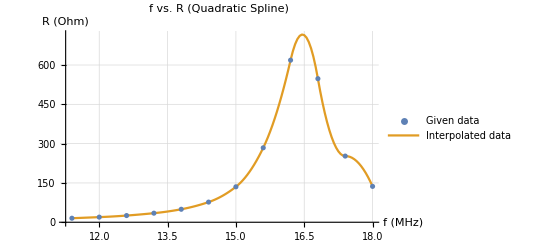

```mathematica
ListPlot[{data1,quads},Joined->{False,True},GridLines->Automatic,PlotLegends->{"Given data","Interpolated data"},AxesLabel->{"f (MHz)","R (Ohm)"},PlotLabel->"f vs. R (Quadratic Spline)"]
```